```mathematica
RemoveFromSets[sets_,n_]:=Select[Map[Select[#,#<n&]&,sets],#≠{}&]
```

```mathematica
RemoveFromSets[{{1,4},{2,6},{3,7},{7}},7]
```

{{1,4},{2,6},{3}}

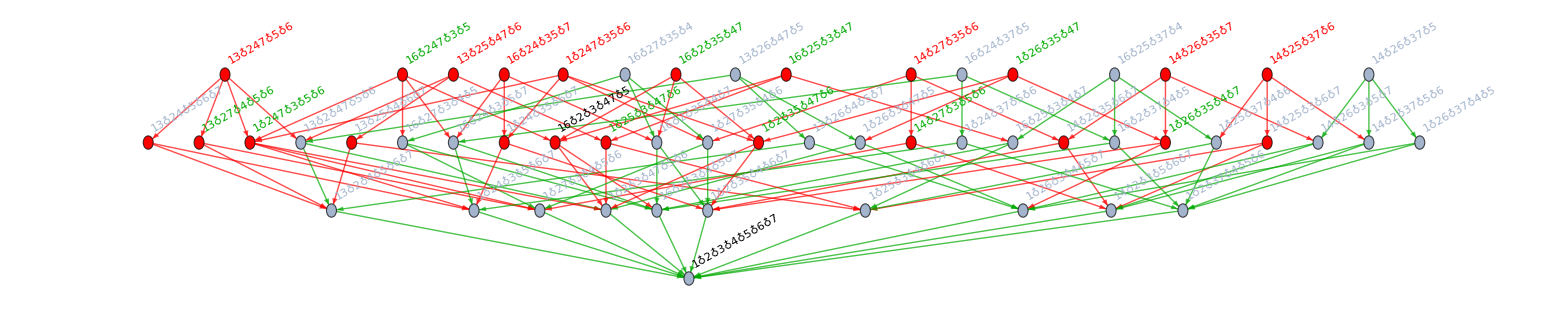
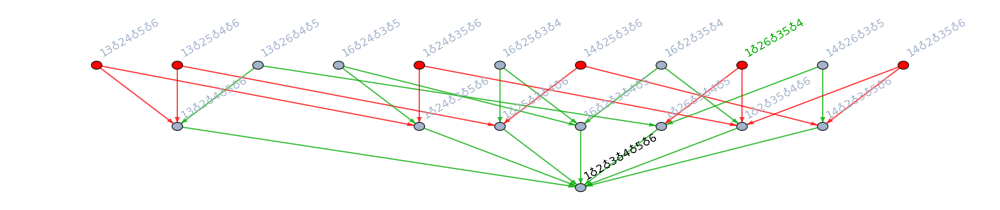
{13♁26♁47,16♁24♁37,16♁27♁35,14♁26♁37,16♁25♁37}→-Graphics-
{13♁26,16♁24,16♁35,14♁26,16♁25}→-Graphics-

```mathematica
Column[
Flatten[
Map[
With[{current=#},
{
ShowQuadsWithImpliedRecursive[current,{ImageSize->1600}],
ShowQuadsWithImpliedRecursive[Map[RemoveFromSets[#,7]&,current],{ImageSize->1000}]}
]&, AllPosibilitiesFor[7,1]]
,1]
]
```

```mathematica
end=VertexList[-Graphics-]
```

{v13x24x5x6,v13x25x4x6,v13x26x4x5,v13x2x4x5x6,v14x25x3x6,v14x26x3x5,v14x2x35x6,v14x2x3x5x6,v16x24x3x5,v16x25x3x4,v16x2x35x4,v16x2x3x4x5,v1x24x35x6,v1x24x3x5x6,v1x25x3x4x6,v1x26x35x4,v1x26x3x4x5,v1x2x35x4x6,v1x2x3x4x5x6}

```mathematica
start=VertexList[-Graphics-]
```

{v13x247x5x6,v13x24x5x6x7,v13x25x47x6,v13x25x4x6x7,v13x26x47x5,v13x26x4x5x7,v13x27x4x5x6,v13x2x47x5x6,v13x2x4x5x6x7,v14x25x37x6,v14x25x3x6x7,v14x26x35x7,v14x26x37x5,v14x26x3x5x7,v14x27x35x6,v14x27x3x5x6,v14x2x35x6x7,v14x2x37x5x6,v14x2x3x5x6x7,v16x247x3x5,v16x24x35x7,v16x24x37x5,v16x24x3x5x7,v16x25x37x4,v16x25x3x47,v16x25x3x4x7,v16x27x35x4,v16x27x3x4x5,v16x2x35x47,v16x2x35x4x7,v16x2x37x4x5,v16x2x3x47x5,v16x2x3x4x5x7,v1x247x35x6,v1x247x3x5x6,v1x24x35x6x7,v1x24x37x5x6,v1x24x3x5x6x7,v1x25x37x4x6,v1x25x3x47x6,v1x25x3x4x6x7,v1x26x35x47,v1x26x35x4x7,v1x26x37x4x5,v1x26x3x47x5,v1x26x3x4x5x7,v1x27x35x4x6,v1x27x3x4x5x6,v1x2x35x47x6,v1x2x35x4x6x7,v1x2x37x4x5x6,v1x2x3x47x5x6,v1x2x3x4x5x6x7}

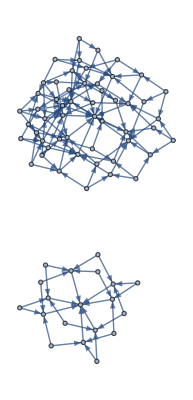

```mathematica
bot=GraphUnion[-Graphics-,-Graphics-]
```

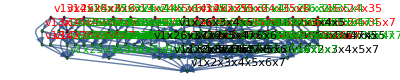

```mathematica
With[{g=GraphUnion[bot,Graph[Graph[Table[
With[{mapped=SetsToSymbol2[RemoveFromSets[SymbolToSets[st],7]]},
mapped ->st
]
,{st,start}
],VertexLabels->"Name"]]]},
Graph[g,GraphLayout->"LayeredDigraphEmbedding", VertexStyle->Table[
vert->If[MemberQ[Flatten[SymbolToSets[vert]],7],Green,Red]
,{vert,VertexList[g]}],
VertexLabels->"Name",
VertexLabelStyle->Table[
vert->With[{sets=SymbolToSets[vert]},If[Length[sets]≥4&&HasQuadrilateralPattern[sets],Darker[Green],If[HasTrianglePattern[sets],Red,Black]] ]
,{vert,VertexList[g]}]]
]
```